## Analytical models of the photophoretic force

© Ben Schafer, Harvard University
Updated March 2025

## Model functions

#### Constants and functions

```mathematica
(* Packages *)
<< StandardAtmosphere`
<< NDSolve`FEM`

(* Physical constants - all SI units *)
physconst={σ-> 5.67*^-8,kb->1.38*^-23,gE->9.8,gM->3.71};
airconstExp = {Sol-> 1366, Alb-> 0, Subscript[T, e]-> 255,m->28.97*^-3/6.02*^23,R->287.058,Subscript[k, bulk]->0.0284,cp->1000,γ->1.4,μ->1.7*^-5};
airconstAtm = {Sol-> 1366,Alb-> 0.3, Subscript[T, e]-> 255, m->28.97*^-3/6.02*^23,R->287.058,Subscript[k, bulk]->0.0284,cp->1000,γ->1.4,μ->1.7*^-5};

(* Atmospheric quantities from the Mathematica database, with ripples removed *)
MFPAtm=Interpolation[Table[{alt,MeanFreePat2h[alt Quantity[, "Kilometers"]][[1]]},{alt,0,110,4}],InterpolationOrder->3] ;
PressAtm=Interpolation[Table[{alt,UnitConvert[Pressure[alt Quantity[, "Kilometers"]],"Pascals"][[1]]},{alt,0,110,4}],InterpolationOrder->3] ;
VelAtm=Interpolation[Table[{alt,MeanParticleSpeed[alt Quantity[, "Kilometers"]][[1]]},{alt,0,110,4}],InterpolationOrder->3] ;TempAtm=Interpolation[Table[{alt,KineticTemperature[alt Quantity[, "Kilometers"]][[1]]},{alt,0,110,4}],InterpolationOrder->3] ;
DenseAtm=Interpolation[Table[{alt,MeanDensity[alt Quantity[, "Kilometers"]][[1]]},{alt,0,110,4}],InterpolationOrder->3] ;

(* Experimental functions *)
GasSelect[Gas_]:=(gasconst=Which[
Gas=="Air",airconstExp,
Gas=="AirAtm",airconstAtm]);
MFPExp[Press_,Temp_,Gas_:"Air"]:=(
GasSelect[Gas];
GasInput=Gas;
(ThermodynamicData[GasInput,"Viscosity",{"Pressure"->Press Quantity[, "Pascals"],"Temperature"->Temp Quantity[, "Kelvins"]}][[1]]/Press)*√(π R Temp/2)/.gasconst);
VelExp[Temp_,Gas_:"Air"]:=(GasSelect[Gas];√((8 kb Temp)/(π m))/.Join[physconst,gasconst]);
```

#### DSMC data for a permeable membrane

Interpolation functions to extend discrete DSMC results to any rarefaction parameter

```mathematica
List200={0.1,0.2,0.5,1,2,5,10,20,50,100,200};
IFuncF[data_,cutoffδ_,fitdatalow_,fitdatahigh_]:=With[{xp:=Log10[dd]},Piecewise[{{1/4(1-fitdatalow[[3]])*fitdatalow[[1]],dd<0.1},{Interpolation[{Log10[#[[1]]],#[[2]]}&/@data][xp],0.1<=dd<=cutoffδ},{(fitdatahigh[[2]]/dd^fitdatahigh[[1]]+fitdatahigh[[3]]),dd>cutoffδ}}]];
IFuncT[data_,cutoffδ_,fitdatalow_,fitdatahigh_]:=With[{xp:=Log10[dd]},Piecewise[{{0,dd<0.1},{Interpolation[{Log10[#[[1]]],#[[2]]}&/@data][xp],0.1<=dd<=cutoffδ},{(fitdatahigh[[2]]/dd^fitdatahigh[[1]]+fitdatahigh[[3]]),dd>cutoffδ}}]];
IFuncB[data_,cutoffδ_,fitdatalow_,fitdatahigh_]:=With[{xp:=Log10[dd]},Piecewise[{{fitdatalow[[3]]/(2*Sqrt[π])*(fitdatalow[[1]]+fitdatalow[[2]](2-fitdatalow[[2]])),dd<0.1},{Interpolation[{Log10[#[[1]]],#[[2]]}&/@data][xp],0.1<=dd<=cutoffδ},{(fitdatahigh[[2]]/dd^fitdatahigh[[1]]+fitdatahigh[[3]]),dd>cutoffδ}}]];

(* Continuum regime: Least-square fit to highest three values of δ *)
ContFit[data2fit_]:=(
Clear[{δ,x,y,z,nlmF,nlmQt,nlmQb}];
nlmF=NonlinearModelFit[data2fit[[All,{1,2}]][[-3;;]],y*δ^-x,{x,y},δ,MaxIterations->500];
nlmQt=NonlinearModelFit[data2fit[[All,{1,3}]][[-3;;]],y*δ^-x+z,{x,{y,0},{z,0}},δ];
nlmQb=NonlinearModelFit[data2fit[[All,{1,4}]][[-3;;]],y*δ^-x+z,{x,{y,0},{z,0}},δ];
Return[{Append[nlmF["BestFitParameters"][[All,2]],0],nlmQt["BestFitParameters"][[All,2]],nlmQb["BestFitParameters"][[All,2]]}]);
```

Load and interpolate DSMC data for helium, with α_n = α_t  = 1

```mathematica
He51=Transpose[{List200,{0.11468, 0.11349, 0.10990 ,0.10185, 0.081647 ,0.04925, 0.028687 ,0.015938 ,0.007083, 0.004620 ,0.002832},{-0.0002, 0.00014, 0.00060,-0.002096,-0.007402,-0.02251,-0.039279,-0.056234,-0.072892,-0.07925,-0.08278},{0.28000, 0.27814 ,0.27249, 0.26372, 0.246169, 0.21141 ,0.17985, 0.151186, 0.123980 ,0.11339, 0.10696}}];
{ForceHe51[dd_],QtHe51[dd_],QbHe51[dd_]}={
IFuncF[He51[[All,{1,2}]],200,{1,1,0.5},ContFit[He51][[1]]],
IFuncT[He51[[All,{1,3}]],200,{1,1,0.5},ContFit[He51][[2]]],
IFuncB[He51[[All,{1,4}]],200,{1,1,0.5},ContFit[He51][[3]]]};
```

#### Hybrid force models

```mathematica
HybridTemps[radvalues_,struxvalues_,envirovalues_,Ddata_,Gas_:"AirAtm",time_:64800]:=(
radconst = {Subscript[ϵ, st]-> radvalues[[1]], Subscript[ϵ, lt]-> radvalues[[2]], Subscript[ϵ, sb]->radvalues[[3]], Subscript[ϵ, lb]->radvalues[[4]],Suns->radvalues[[5]]};
struxconst={w->struxvalues[[1]],β->struxvalues[[2]],H->struxvalues[[3]],ad->struxvalues[[4]],r->struxvalues[[5]],Subscript[α, t]->struxvalues[[6]],Subscript[α, b]->struxvalues[[7]]};
gasconst=GasSelect[Gas];
Which[Gas=="AirAtm",
enviroconst = {v-> VelAtm[envirovalues[[1]]], P->PressAtm[envirovalues[[1]]], T->TempAtm[envirovalues[[1]]],MFP->MFPAtm[envirovalues[[1]]]};
{LongTop,LongBot}={Subscript[ϵ, lt]((1-Subscript[ϵ, lb]) σ Subscript[T, e]^4+Subscript[ϵ, lb] σ Tb^4-2 σ Tt^4),Subscript[ϵ, lb] (σ Subscript[T, e]^4+Subscript[ϵ, lt] σ Tt^4-2 σ Tb^4)};,
Gas≠"AirAtm",
enviroconst={P->envirovalues[[1]], T->envirovalues[[2]],v-> VelExp[envirovalues[[1]],Gas], MFP->MFPExp[envirovalues[[1]],envirovalues[[2]],Gas]};{LongTop,LongBot}={Subscript[ϵ, lt]((1+(1-Subscript[ϵ, lb]))σ T^4+Subscript[ϵ, lb] σ Tb^4-2 σ Tt^4),Subscript[ϵ, lb] ((1+(1-Subscript[ϵ, lt]))σ T^4+Subscript[ϵ, lt] σ Tt^4-2 σ Tb^4)};];
allconst=Join[radconst,struxconst,enviroconst,gasconst,physconst];
HalfWave=Sin[(2π time)/(3600*24)-π];
If[Positive[HalfWave],{SolarTop=Suns*Sol Subscript[ϵ, st](1+Alb (1-Subscript[ϵ, sb]))HalfWave,SolarBot=Suns*Sol Subscript[ϵ, sb](Alb+(1-Subscript[ϵ, st])) HalfWave},{SolarTop=0,SolarBot=0}];
{Subscript[RF, t], Subscript[RF, b]}={SolarTop+LongTop,SolarBot+LongBot};
δ=r/MFP/.allconst;
Qt=((((γ+1)/(γ-1))/4)Ddata[[2]][δ]*P*v/T)/.allconst; (* Units W/(m^2 K), prefactor w/ γ adjusts for polyatomics, must multiply by Tb-Tt to get true heat flux*);
Qb=(Ddata[[3]][δ]*P*v/T)/.allconst; (* Units W/(m^2 K), must multiply by Tb-Tt to get true heat flux*);
Qm=((Subscript[k, bulk]/H)^-1+((γ+1)/(γ-1)(P v Subscript[α, t] Subscript[α, b])/(8T(Subscript[α, t]+ Subscript[α, b])))^-1)^-1; (* Bird says the free-molecular prefactor is 1/4Sqrt[π], Madhusudana says 1/8 *);
E1=Subscript[RF, t]+Subscript[RF, b]==(Qb+Qt)(Tb-Tt);(* W/m^2*)
E2=((Subscript[RF, b]-Qb(Tb-Tt))-(Subscript[RF, t]- Qt(Tb-Tt)))*(1-β)==(Tb-Tt) (Qm*(1-β-w)+1.8*w/H );
list=NSolve[E1 && E2/.allconst, {Tb, Tt},PositiveReals];
Return[list[[1]]] (* Sort to return the correct answer first *))
HybridForce[radvalues_,struxvalues_,envirovalues_,Ddata_,Gas_:"AirAtm",time_:64800]:=(
Solns=HybridTemps[radvalues,struxvalues,envirovalues,Ddata,Gas,time];
ΔT=Tb-Tt;
Return[100*(Ddata[[1]][δ]*P ΔT )/T/.Join[Solns,allconst]]) (* In units g/m^2 *)
HybridForceAvg[radvalues_,struxvalues_,envirovalues_,Ddata_,Gas_:"AirAtm"] :=HybridForce[radvalues,struxvalues,envirovalues,Ddata,Gas,0]*(1-1/π)+HybridForce[radvalues,struxvalues,envirovalues,Ddata,Gas,68400]*1/π
```

## Lofting force calculations

Calculate the area photophoretic lofting force (in g/m^2) of a structure in the atmosphere with following parameters:
-  Altitude of 70 km 
- Peak daytime 
- 1 cm radius structure  
- β = 0.5 
- ϵ_(IR,b) = ϵ_(vis,t) = 0.01 (to avoid divergence) and ϵ_(vis,b) = ϵ_(IR,t) = 1
- α_n=α_t=1 
- H = 125 µm
- w = 0 everywhere

```mathematica
HybridForce[{0.01,1,1,0.01,1},{0,0.5,125*^-6,0,0.01,1,1},{70},{ForceHe51,QtHe51,QbHe51},"AirAtm",68400]
```

28.8793

Calculate the area lofting force of the same structure in the testing chamber, assuming:
- Air is used as the surrounding gas
- 5 Pa pressure
- 293 K ambient pressure 
- Structure is illuminated with 2 solar constants

```mathematica
HybridForce[{0.01,1,1,0.01,2},{0,0.5,125*^-6,0,0.01,1,1},{5,293},{ForceHe51,QtHe51,QbHe51},"Air"]
```

51.3372

## 2D temperature models

#### Microscale

Spacing between holes is a = u/(1+ Sqrt[3]) = (s Sqrt[3]) / (1+ Sqrt[3])
Hexagon side length is s = u / Sqrt[3]

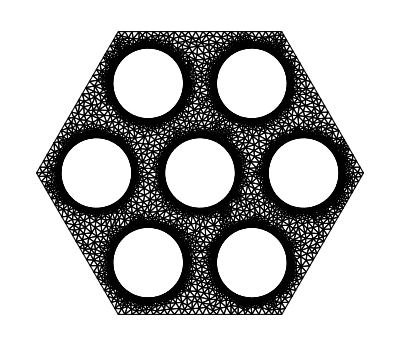

```mathematica
hspec=Sqrt[3]/(1+Sqrt[3]);
ΩHex[s_,rpost_]:=RegionDifference[
Polygon[{{1,0},{1/2,Sqrt[3]/2},{-1/2,Sqrt[3]/2},{-1,0},{-1/2,-Sqrt[3]/2},{1/2,-Sqrt[3]/2}}*s],
RegionUnion[Disk[{0,0}*s,rpost],Disk[{1,0}*s*hspec,rpost],Disk[{1/2,Sqrt[3]/2}*s*hspec,rpost],Disk[{-1/2,Sqrt[3]/2}*s*hspec,rpost],Disk[{-1,0}*s*hspec,rpost],Disk[{-1/2,-Sqrt[3]/2}*s*hspec,rpost],Disk[{1/2,-Sqrt[3]/2}*s*hspec,rpost]]];
refinementFunction[s_,radius_]:=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices]; If[Sqrt[x^2+y^2]>1.1*radius&&Sqrt[(x-s*hspec)^2+y^2]>1.1*radius&&Sqrt[(x+s*hspec)^2+y^2]>1.1*radius&&Sqrt[(x-0.5*s*hspec)^2+(y-Sqrt[3]/2*s*hspec)^2]>1.1*radius&&Sqrt[(x-0.5*s*hspec)^2+(y+Sqrt[3]/2*s*hspec)^2]>1.1*radius&&Sqrt[(x+0.5*s*hspec)^2+(y-Sqrt[3]/2*s*hspec)^2]>1.1*radius&&Sqrt[(x+0.5*s*hspec)^2+(y+Sqrt[3]/2*s*hspec)^2]>1.1*radius,area>0.001*s^2,area>0.00003*s^2]]];
meshfunc[s_,rpost_]:=ToElementMesh[ΩHex[s,rpost],MaxCellMeasure->.001*s^2,MeshRefinementFunction->refinementFunction[s,rpost]];
mesh=meshfunc[100*^-6/Sqrt[3],12.5*^-6];(* s = u/Sqrt[3] *)
mesh["Wireframe"]
```

```mathematica
TempSolverH[radvalues_,struxvalues_,envirovalues_,Ddata_,tf_,s_,rpost_,centerT_,posts_:True,Gas_:"Air",time_:64800]:=((*First define the vertical conduction through the air and the solid posts.*)
Tsoln=HybridTemps[radvalues,struxvalues,envirovalues,Ddata,Gas,time];
Tbar=(Tb+Tt)/2/.Tsoln;(* Using the 1D model, compute the average temperature of the top and bottom face-sheets *);
LongTop=Subscript[ϵ, lt]((1+(1-Subscript[ϵ, lb]))σ T^4+Subscript[ϵ, lb] σ (Tbar^4+4 Tbar^3 ΔT[x,y]/2)-2 σ (Tbar^4-4 Tbar^3 ΔT[x,y]/2));
LongBot=Subscript[ϵ, lb] ((1+(1-Subscript[ϵ, lt]))σ T^4+Subscript[ϵ, lt] σ (Tbar^4-4 Tbar^3 ΔT[x,y]/2)-2 σ (Tbar^4+4 Tbar^3 ΔT[x,y]/2));
{Subscript[RF, t], Subscript[RF, b]}={SolarTop+LongTop,SolarBot+LongBot}; (* Linearized radiative terms *); 
{kface,kpost}={1.8,1.8}; (* Assume all posts are just solid cylinders with radius tf *)
(*Define where each conduction term applies in the domain.*)
If[posts==True,cond=Piecewise[{{Qm,Sqrt[x^2+y^2]>rpost+tf&&Sqrt[(x-s*hspec)^2+y^2]>rpost+tf&&Sqrt[(x+s*hspec)^2+y^2]>rpost+tf&&Sqrt[(x-0.5*s*hspec)^2+(y-Sqrt[3]/2*s*hspec)^2]>rpost+tf&&Sqrt[(x-0.5*s*hspec)^2+(y+Sqrt[3]/2*s*hspec)^2]>rpost+tf&&Sqrt[(x+0.5*s*hspec)^2+(y-Sqrt[3]/2*s*hspec)^2]>rpost+tf&&Sqrt[(x+0.5*s*hspec)^2+(y+Sqrt[3]/2*s*hspec)^2]>rpost+tf}},kpost/H],
cond=Qm];
eps=10^-8;
u=Sqrt[3]*s;
pbcs={PeriodicBoundaryCondition[ΔT[x,y],Abs[y-(x+s)*Sqrt[3]]<=eps,TranslationTransform[{3s/2,-u/2}]],(*top left to bottom right*)
PeriodicBoundaryCondition[ΔT[x,y],Abs[y+u/2]<=eps,TranslationTransform[{0,u}]],(*bottom to top*)
PeriodicBoundaryCondition[ΔT[x,y],Abs[y-(-x-s)*Sqrt[3]]<=eps,TranslationTransform[{3s/2,u/2}]](*bottom left to top right*)};
NDSolve[{(Subscript[RF, b]-Subscript[RF, t])+kface*tf*Laplacian[ΔT[x,y],{x,y}]-(2cond+Qb-Qt)*ΔT[x,y]==0,pbcs,DirichletCondition[ΔT[x,y]==0,x==0&&y==0]}/. allconst,ΔT,{x,y}∈mesh])

(*A function to plot the result*)
TempPlotH[radvalues_,struxvalues_,envirovalues_,Ddata_,tf_,s_,rpost_,centerT_,posts_:True,Gas_:"Air",time_:64800]:=(
soln=TempSolverH[radvalues,struxvalues,envirovalues,Ddata,tf,s,rpost,centerT,posts,Gas,time];
Show[DensityPlot[Evaluate[(ΔT[x/10^6,y/10^6]/. soln[[1]])],{x,-s*10^6,s*10^6},{y,-s*10^6,s*10^6},PlotRange->All,PlotPoints->100,AspectRatio->Automatic,MaxRecursion->2,PlotLegends->Automatic,Frame->True,GridLines->Automatic,ColorFunction->"TemperatureMap",FrameStyle->Directive[Black,12],FrameLabel->Map[Style[#,Black,16]&,{"x (μm)","y (μm)","ΔT"}],Epilog->{Dashed,Line[s*10^6*{{1,0},{1/2,Sqrt[3]/2},{-1/2,Sqrt[3]/2},{-1,0},{-1/2,-Sqrt[3]/2},{1/2,-Sqrt[3]/2},{1,0}}]}]])
```

NDSolve::bcnop: No places were found on the boundary where x==0&&y==0 was True, so DirichletCondition[ΔT==0,x==0&&y==0] will effectively be ignored.

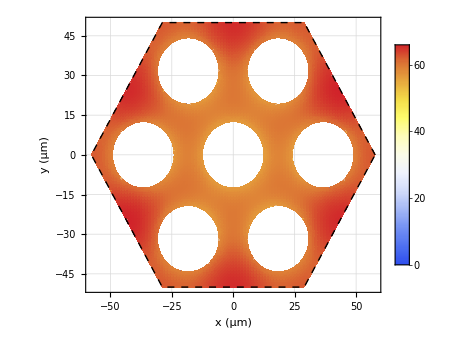

```mathematica
TempPlotH[{0.01,0.99,0.99,0.01,1},{0,0.5,125*^-6,0,0.03,1,1},{5,250},{ForceHe51,QtHe51,QbHe51},10^-7,100*^-6/Sqrt[3],12.5*^-6,0]
```

#### Macroscale

```mathematica
{rchamb=0.15,hchamb=0.2,rdisk=0.01,hdisk=0.0001,DTop=2301.13,DBot=-1751.66};
domain=RegionDifference[Rectangle[{0,-hchamb/2},{rchamb,hchamb/2}],Rectangle[{0,-hdisk/2},{rdisk,hdisk/2}]];
macromesh=ToElementMesh[domain,MeshRefinementFunction->Function[{vertices,area},Block[{r,z},{r,z}=Mean[vertices];
If[r<=2 rdisk&&z^2<=rdisk^2,area>0.0000001,area>0.01]]]];
BCs={DirichletCondition[T[r,z]==293,r==rchamb||z^2==(hchamb/2)^2]};
Soln=NDSolve[{D[T[r,z],{r,2}]+(1/r) D[T[r,z],r]+D[T[r,z],{z,2}]==NeumannValue[DTop,r<rdisk&&z==hdisk/2]+NeumannValue[DBot,r<rdisk&&z==-hdisk/2]+NeumannValue[DBot-DTop*((z+hdisk/2)/hdisk),r==rdisk&&z^2<=(hdisk/2)^2],BCs},T,{r,z}∈macromesh];
{ContourPlot[Evaluate[T[r/1000,z/1000]/. Soln],{r,0,2 rdisk*1000},{z,-20* hdisk*1000,20*hdisk*1000},Contours->500,ContourStyle->None,ColorFunction->"TemperatureMap",FrameLabel->{"x (mm)","z (mm)"}],ContourPlot[Evaluate[T[r/1000,z/1000]/. Soln],{r,0,rchamb*1000},{z,-hchamb/2*1000,hchamb/2*1000},Contours->500,ContourStyle->None,ColorFunction->"TemperatureMap",FrameLabel->{"x (mm)","z (mm)"}]}
```

{-Graphics-,-Graphics-}